```mathematica
FName[name_,p_,q_,d_]:=NotebookDirectory[]<>name<>"_"<>ToString[p]<>"_"<>ToString[q]<>If[d>=p+q,"","_"<>ToString[d]];
irrepDims[p_,q_,d_]:=irrepDims[p,q,d]= Import[FName["idempotents/metadata",p,q,d]<>".m"][[1]];
```

```mathematica
(* Transpose a Brauer diagram *)
BT[σ_]:=SortB[B[Sequence@@(FlipPair[#,0]&/@(σ/.B->List))]];
(* Sort the diagram description to make it canonical *)
SortB[σ_]:=Sort@Map[Sort,σ,1];
(*Given the line defined by a pair of vertices, flip the vertices which are located after the wall at level p*)
FlipPair[pair_,p_]:=Sort@(If[Abs[#]>p,-#,#]&/@pair);
(*Generate Walled Brauer Algebra generators*)
WalledBrauerGenerators[p_,q_]:=WalledBrauerGenerators[p,q]=B[Sequence@@#]&/@Map[FlipPair[#,p]&,FoldList[ReplacePart[#1,#2->{-#2,#1[[#2]]}]&,#,Range[p+q]][[-1]]&/@Table[Range[i-1]~Join~{i+1,i}~Join~Range[i+2,p+q],{i,1,p+q-1}],{2}];
(*Generate Walled Brauer Algebra basis*)
WalledBrauerBasis[p_,q_]:=WalledBrauerBasis[p,q]=(SortB[B[Sequence@@#]])&/@Map[FlipPair[#,p]&,FoldList[ReplacePart[#1,#2->{-#2,#1[[#2]]}]&,#,Range[p+q]][[-1]]&/@Permutations[Range[p+q]],{2}];
```

```mathematica
(* Contract a Brauer diagram at one fixed position l *)
ContractDiag[diag__,{l_,d_}]:=Module[{new,data},
data=diag/.B->List;
new=Sort@Flatten@Table[If[data[[i]]∩{-l,l}!={},Complement[data[[i]],{-l,l}],{}],{i,1,Length@data}];
If[new=={},d SortB[B[Sequence@@Sort@Table[If[data[[i]]∩{-l,l}!={},Nothing,data[[i]]],{i,1,Length@data}]]], SortB[B[Sequence@@Sort@(Table[If[data[[i]]∩{-l,l}!={},Nothing,data[[i]]],{i,1,Length@data}]~Join~{new})]]]
];
(* Contract a lin. comb. of Brauer diagrams x at one fixed position l *)
ContractOne[x_,{l_,d_}]:=x/.B[lst__]:>ContractDiag[{lst},{l,d}];
(* Contract a lin. comb. of Brauer diagrams x at fixed positions lst *)
Contract[x_,lst_List,d_]:=Fold[ContractOne,x,{lst,ConstantArray[d,Length@lst]}ᵀ];
(* Compute the full trace of a lin. comb. of Brauer diagrams x *)
FullContract[x_,p_,q_,d_]:=Contract[x,Table[i,{i,p+q}],d]/.B[]->1;
(* Same functions, but for 2 registers *)
ContractOne2[x_,{l_,d_}]:=If[l>=p+q+1,x/.(B[lst1__]⊗B[lst2__]:>B[lst1]⊗ContractDiag[{lst2},{l-p+q,d}]),x/.(B[lst1__]⊗B[lst2__]:>ContractDiag[{lst1},{l,d}]⊗B[lst2])];
Contract2[x_,lst_List,d_]:=Fold[ContractOne2,x,{lst,ConstantArray[d,Length@lst]}ᵀ]/.B[]->1;
FullContract2[x_,p_,q_,d_]:=FullContract[Contract2[x,Range[(p+q)],d]/.B[]->1,d];
```

```mathematica
(* Multiply two Brauer algebra diagrams *)
MultiplyPair2[σ1_,σ2_,d_]:=Module[{lst,i,new,pos,σ1n,σ2n},
σ1n=Map[If[#<0,Subscript[b, -#],Subscript[a, #]]&,List@@σ1,{2}];
σ2n=Map[If[#<0,Subscript[b, -#],Subscript[a, #]]&,List@@σ2,{2}];
(* Denote the nodes in the middle layer by x *)
lst=Join[σ1n/.b->x,σ2n/.a->x];
(* Treat each node Subscript[x, i] in the intermediate level *)
Do[
(* Find all edges containing Subscript[x, i] *)
new=lst⟦pos=Position[lst,Subscript[x, i],{2}]⟦All,1⟧⟧;
(* Update the list by removing these edges and adding a new one *)
lst=Append[Delete[lst,List/@pos],DeleteCases[Join@@new,Subscript[x, i]]];
,{i,1,Length[σ1]}
];
(* Output the new Brauer diagram and the normalization factor from the number of loops *)
{B@@SortB@Map[If[TrueQ[First[#]==b],-Part[#,2],Part[#,2]]&,DeleteCases[lst,{}],{2}],d^Count[lst,{}]}
];
(* Multiply two Brauer algebra diagrams *)
MultiplyPair[σ1_,σ2_,d_]:=Times@@MultiplyPair2[σ1,σ2,d];
```

```mathematica
(* Convert integer to a string and padd with 0s *)
Str[i_,max_]:=StringJoin@@(ToString/@IntegerDigits[i,10,IntegerLength@max]);
(* Shorter variable names that also account for symmetry *)
x[λ_,μ_,i_,j_,k_,l_,dB_]:=Symbol["x"<>Str[λ,Length@dB]<>Str[μ,Length@dB]<>StringJoin@@Sort[{Str[i,dB⟦λ⟧]<>Str[k,dB⟦μ⟧],Str[j,dB⟦λ⟧]<>Str[l,dB⟦μ⟧]}]];
```

```mathematica
(* Diagram multiplication tensor *)
prodRule[p_,q_,d_,i_,j_]:=Block[{basis=WalledBrauerBasis[p,q],prod},prod=MultiplyPair2[basis[[i]],basis[[j]],d];{i,j,Position[basis,prod[[1]]][[1,1]]}->prod[[2]]];
mulTensor[p_,q_,d_]:=mulTensor[p,q,d]=SparseArray[Flatten@Table[prodRule[p,q,d,i,j],{i,1,(p+q)!},{j,1,(p+q)!}],{(p+q)!,(p+q)!,(p+q)!}];

(* Diagram contraction tensor *)
contractTensor[p_,q_,d_]:=contractTensor[p,q,d]=Table[FullContract[WalledBrauerBasis[p,q][[i]],p,q,d],{i,1,(p+q)!}];
contractTensor[p_,q_,d_,lst_]:=contractTensor[p,q,d,lst]=Table[(Contract[WalledBrauerBasis[p,q][[i]],lst,d]/.{(B[y__]:>B[Sequence@@({y}/.Flatten[{#[[1]]->#[[2]],-#[[1]]->-#[[2]]}&/@({Complement[Range[p+q],lst],Range[p+q-Length[lst]]}ᵀ)])])})
/.{B[]:>1,B[arg__]:>SparseArray[{Position[WalledBrauerBasis[p-Count[lst,x_/;x<=p],q-Count[lst,x_/;x>p]],B[arg],{1}][[1,1]]}->1,(p+q-Length[lst])!]},{i,1,(p+q)!}]ᵀ;

(* Diagram contraction and adding Id tensor *)
contractIdTensor[p_,q_,d_,lstContract_,lstId_]:=contractIdTensor[p,q,d,lstContract,lstId]=Table[(Contract[WalledBrauerBasis[p,q][[i]],lstContract,d]/.(B[y___]:>SortB@B[Sequence@@({y,Sequence@@({-#,#}&/@lstId)}/.Flatten[{#[[1]]->#[[2]],-#[[1]]->-#[[2]]}&/@({Complement[Range[p+q],Complement[lstContract,lstId]],Range[p+q-Length[lstContract]+Length[lstId]]}ᵀ)])]))/.
{B[]:>1,B[arg__]:>SparseArray[{Position[WalledBrauerBasis[p-Count[Complement[lstContract,lstId],x_/;x<=p],q-Count[Complement[lstContract,lstId],x_/;x>p]],B[arg],{1}][[1,1]]}->1,(p+q-Length[lstContract]+Length[lstId])!]}
,{i,1,(p+q)!}]ᵀ

(* Auxilary tensors *)
mulTensorMatrix[p_,q_,d_]:=mulTensorMatrix[p,q,d]=Flatten[mulTensor[p,q,d],{{1,2},{3}}];
MulContractTensor[p_,q_,d_]:=MulContractTensor[p,q,d]=ArrayReshape[mulTensorMatrix[p,q,d].contractTensor[p,q,d],{(p+q)!,(p+q)!}]
```

```mathematica
(* Operations od 1vecs *)
FullContractVec[vec_,p_,q_,d_]:=(contractTensor[p,q,d].{vec}ᵀ)[[1]]
MultiplyVecs[vec1_,vec2_,p_,q_,d_]:=Flatten[KroneckerProduct[vec1,vec2]].mulTensorMatrix[p,q,d]
MultiplyVecs[vec1_,vec2_,vec3_,p_,q_,d_]:=MultiplyVecs[vec1,MultiplyVecs[vec2,vec3,p,q,d],p,q,d]

(*Define psd constraints and make them symmetric*)
psd[λ_,μ_,p_,q_,d_]:=psd[λ,μ,p,q,d]=Flatten[Table[x[λ,μ,i,j,k,l,irrepDims[p,q,d]],{i,1,irrepDims[p,q,d]⟦λ⟧},{k,1,irrepDims[p,q,d]⟦μ⟧},{j,1,irrepDims[p,q,d]⟦λ⟧},{l,1,irrepDims[p,q,d]⟦μ⟧}],{{1,2},{3,4}}];

(*Contract vec, which has the form ∑KroneckerProduct[*,*] on given list of indices *)
Contract2Vec[vec_,p_,q_,d_,lst_]:=contractTensor[q,p,d,Select[lst,#<=(p+q)&]].vec.contractTensor[p,q,d,Select[lst,#>(p+q)&]-(p+q)]ᵀ
Contract2Vec[vec_,p_,q_,d_]:=Contract2Vec[vec,p,q,d,Range[2(p+q)]]
```

```mathematica
(* Realise linear constraints *)
Psys[p_,q_]:={1};
Osys[p_,q_]:=Range[2,p+q];
Isys[p_,q_]:=Range[p+q+1,2(p+q)-1];
Fsys[p_,q_]:={2(p+q)};

Choi[ansatz_,i_,p_,q_,d_]:=If[i<p+q,Expand[If[i==0,Contract2Vec[ansatz,p,q,d],Contract2Vec[ansatz,p,q,d,Osys[p,q][[i;;p+q-1]]~Join~Isys[p,q][[i+1;;p+q-1]]~Join~Fsys[p,q]]]/d^(p+q-i)],ansatz]

TrChoi[ansatz_,i_,p_,q_,d_]:=If[i==0,Print["Error: i should be >0"],Expand[Contract2Vec[ansatz,p,q,d,Osys[p,q][[i;;p+q-1]]~Join~Isys[p,q][[i;;p+q-1]]~Join~Fsys[p,q]]/d^(p+q-i)]]

ChoiTensorId[ansatz_,i_,p_,q_,d_]:=Expand[If[i>=1,
contractIdTensor[q,p,d,Osys[p,q][[i;;p+q-1]],Osys[p,q][[i;;i]]].ansatz.contractTensor[p,q,d,(Isys[p,q][[i+1;;p+q-1]]~Join~Fsys[p,q])-(p+q)]ᵀ,
contractIdTensor[q,p,d,Osys[p,q]~Join~Psys[p,q],Psys[p,q]].ansatz.contractTensor[p,q,d,(Isys[p,q][[i+1;;p+q-1]]~Join~Fsys[p,q])-(p+q)]ᵀ
]/d^(p+q-i)]
```

```mathematica
(* Load blocks *)
ClearAll[blocksLoad,blocksLoadN]
blocksLoad[p_,q_,d_]:=blocksLoad[p,q,d]=Import[FName["blocks/blocks",p,q,d]<>".m"]
blocksLoadN[p_,q_,d_,prec_]:=blocksLoadN[p,q,d,prec]=N[blocksLoad[p,q,d],prec]

(* Map 2vec to selected blocks *)
vec2ToBlocks[vec_,λ_,μ_,pλ_,qλ_,pμ_,qμ_,d_]:=Sum[vec[[i,j]]KroneckerProduct[blocksLoad[pλ,qλ,d][[i,λ]],blocksLoad[pμ,qμ,d][[j,μ]]],{i,1,(pλ+qλ)!},{j,1,(pμ+qμ)!}]
vec2ToBlocksN[vec_,λ_,μ_,pλ_,qλ_,pμ_,qμ_,d_,prec_]:=Sum[vec[[i,j]]KroneckerProduct[blocksLoadN[pλ,qλ,d,prec][[i,λ]],blocksLoadN[pμ,qμ,d,prec][[j,μ]]],{i,1,(pλ+qλ)!},{j,1,(pμ+qμ)!}]

(* Map 2vec to selected blocks *)
vec2ToBlocksBetter[vec_,λ_,μ_,pλ_,qλ_,pμ_,qμ_,d_]:=Flatten[vec].Flatten[Outer[KroneckerProduct,blocksLoad[pλ,qλ,d][[All,λ]],blocksLoad[pμ,qμ,d][[All,μ]],1],{{1,2},{3},{4}}]
vec2ToBlocksBetterN[vec_,λ_,μ_,pλ_,qλ_,pμ_,qμ_,d_,prec_]:=Flatten[vec].Flatten[Outer[KroneckerProduct,blocksLoadN[pλ,qλ,d,prec][[All,λ]],blocksLoadN[pμ,qμ,d,prec][[All,μ]],1],{{1,2},{3},{4}}]
```

```mathematica
cyclicDiag[n_]:=SortB[B[Sequence@@(FoldList[ReplacePart[#1,#2->{-#2,#1[[#2]]}]&,PermutationList[Cycles[{Range[n]}]],Range[n]][[-1]])]];
shiftTensor[p_,q_,d_]:=SparseArray[Table[{i,Position[WalledBrauerBasis[q,p],MultiplyPair[cyclicDiag[p+q],MultiplyPair[WalledBrauerBasis[p,q][[i]],BT@cyclicDiag[p+q],d],d]][[1,1]]}->1,{i,1,(p+q)!}],{(p+q)!,(p+q)!}]
shiftVec[vec_,p_,q_,d_]:=vec.shiftTensor[p,q,d]
```

```mathematica
{p,q,d}={1,1,3};
Print["{p, q, d} = ",{p,q,d}]
Print["Dimensions of simple (𝒜^d)_(p, q)-modules = ",irrepDims[p,q,d]]
```

{p, q, d} = {1,1,3}

Dimensions of simple (𝒜^d)_(p, q)-modules = {1,1}

```mathematica
ε=Import[FName["idempotents/elementary",p,q,d]<>".m"];
εLeft=Import[FName["idempotents/elementary",q,p,d]<>".m"];
dimλU=Table[FullContractVec[ε[[λ,1,1]],p,q,d],{λ,1,Length@irrepDims[p,q,d]}];
```

```mathematica
(*Generate the ansatz via eq. (13) in arXiv:2209.02907*)
ansatz=Expand@ParallelSum[(x[λ,μ,i,j,k,l,irrepDims[p,q,d]])KroneckerProduct[εLeft[[λ,i,j]],ε[[μ,k,l]]],{λ,1,Length@irrepDims[p,q,d]},{μ,1,Length@irrepDims[p,q,d]},{i,1,irrepDims[p,q,d]⟦λ⟧},{j,1,irrepDims[p,q,d]⟦λ⟧},{k,1,irrepDims[p,q,d]⟦μ⟧},{l,1,irrepDims[p,q,d]⟦μ⟧}];
```

```mathematica
ansatzNumeric=N[ansatz,50];
```

```mathematica
(*Export[FName["app4_data/ansatz",p,q,d]<>".m",ansatzNumeric]*)
```

```mathematica
(*(*Load the above ansatz from the memory*)
ansatz=Import[NotebookDirectory[]<>"app4_data/ansatz_normal_"<>ToString[p]<>"_"<>ToString[q]<>"_"<>ToString[d]<>".m"]/.symSol[p,q,d];*)
```

```mathematica
(*ansatzNumeric=Import[FName["app4_data/ansatz",p,q,d]<>".m"];*)
```

```mathematica
(*Generate the matrix Ω from eq. (18) in arXiv:2209.02907 shiftVec[ε[[λ,i,j]],p,q,d],ε[[λ,i,j]]*)
Ω=Sum[1/d^2 1/dimλU[[λ]] KroneckerProduct[shiftVec[ε[[λ,i,j]],p,q,d],ε[[λ,i,j]]],{λ,1,Length[irrepDims[p,q,d]]},{i,1,irrepDims[p,q,d]⟦λ⟧},{j,1,irrepDims[p,q,d]⟦λ⟧}];
```

```mathematica
Timing[M=MulContractTensor[p,q,d]ᵀ.Ωᵀ.MulContractTensor[p,q,d];]
Timing[objective=Chop@Total@Expand[Flatten[Mᵀ]*Flatten[ansatzNumeric]];]
objective
```

{0.000265,Null}

{0.000128,Null}

2.0833333333333333333333333333333333333333333333333 x111111+0.08333333333333333333333333333333333333333333333333 x121111+0.08333333333333333333333333333333333333333333333333 x211111+0.022727272727272727272727272727272727272727272727273 x221111

```mathematica
(*************************************************)
```

```mathematica
Timing[M=MulContractTensor[p,q,d]ᵀ.Ωᵀ.MulContractTensor[p,q,d];]
Timing[ansatzNumericElim=Chop@Expand[ansatzNumeric/.elim];]
Timing[objective=Chop@Total@Expand[Flatten[Mᵀ]*Flatten[ansatzNumericElim]];]
```

{0.000196,Null}

{0.000059,Null}

{0.000094,Null}

```mathematica
(*************************************************)
```

```mathematica
Timing[Chop@Expand@vec2ToBlocksBetterN[eqConstrRaw[[p+q]],2,3,p+q-q,q,p+q-1,0,d];]
Timing[Chop@Expand@vec2ToBlocksN[eqConstrRaw[[p+q]],2,3,p+q-q,q,p+q-1,0,d];]
```

{0.001385,Null}

{0.001103,Null}

```mathematica
(*************************************************)
```

```mathematica
eqConstrRaw=Table[PrintTemporary[i];Chop[TrChoi[ansatzNumeric,i,p,q,d]-ChoiTensorId[ansatzNumeric,i-1,p,q,d]],{i,1,p+q}];
```

```mathematica
Timing[eqConstr=Chop@Flatten[{Choi[ansatzNumeric,0,p,q,d]-1}~Join~eqConstrRaw[[1;;2]]~Join~Table[PrintTemporary[i];Table[PrintTemporary[{λ,μ,irrepDims[q,i-q,d]⟦λ⟧*irrepDims[i-1,0,d]⟦μ⟧}];Expand@vec2ToBlocksBetterN[eqConstrRaw[[i]],λ,μ,q,i-q,i-1,0,d,50],{λ,1,Length[irrepDims[q,i-q,d]]},{μ,1,Length[irrepDims[i-1,0,d]]}],{i,3,p+q}]];]
```

{0.000274,Null}

```mathematica
(*************************************************)
```

```mathematica
eqConstr/.x__Real:>RootApproximant[x];
```

```mathematica
eqConstr=Import[FName["app4_data/eq",p,q,d]<>"_exact.m"];
```

```mathematica
eqConstrExact=Import[FName["app4_data/eq",p,q,d]<>"_exact.m"];
```

```mathematica
eqConstrExact/.guessAnsatz//Simplify
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Solve[(#==0)&/@Union@FullSimplify@Union@(eqConstrExact/.guessAnsatz)]
```

{{a1→-(√5)/4,a2→(√(3/2))/2,a3→-1/(2 √2),a4→-1/(2 √6),a5→-1/(4 √3)}}

```mathematica
(***************************************)
```

```mathematica
elim={x111111->0,x121111->0,x121112->0,x121113->0,x121213->0,x121313->0,x131112->0,x131212->0,x211111->0,x211121->0,x211131->0,x212121->0,x212131->0,x213131->0,x221111->0,x221112->0,x221113->0,x221121->0,x221122->0,x221123->0,x221131->0,x221132->0,x221133->0,x221213->0,x221221->0,x221222->0,x221223->0,x221231->0,x221232->0,x221233->0,x221313->0,x221321->0,x221322->0,x221323->0,x221331->0,x221332->0,x221333->0,x222121->0,x222122->0,x222123->0,x222131->0,x222132->0,x222133->0,x222223->0,x222232->0,x222323->0,x222331->0,x222332->0,x222333->0,x223132->0,x223232->0,x223233->0,x231112->0,x231121->0,x231122->0,x231131->0,x231132->0,x231212->0,x231221->0,x231222->0,x231231->0,x231232->0,x232121->0,x232122->0,x232131->0,x232132->0,x232222->0,x232231->0,x232232->0,x233131->0,x233132->0,x233232->0,x311111->0,x311121->0,x321111->0,x321112->0,x321113->0,x321121->0,x321122->0,x321123->0,x321212->0,x321213->0,x321221->0,x321222->0,x321223->0,x321313->0,x321321->0,x321322->0,x321323->0,x322122->0,x322123->0,x322222->0,x322223->0,x322323->0,x331112->0,x331121->0,x331212->0,x331221->0,x331222->0,x332121->0,x332122->0,};
```

```mathematica
(*************************************************)
```

```mathematica
elim={};
```

```mathematica
psdElim[λ_,μ_,p_,q_,d_]:=Chop@Expand[psd[λ,μ,p,q,d]/.elim];
```

```mathematica
psdConstr=Flatten@Table[VectorGreaterEqual[{psdElim[λ,μ,p,q,d],0},{"SemidefiniteCone",irrepDims[p,q,d]⟦λ⟧*irrepDims[p,q,d]⟦μ⟧ }],{λ,1,Length@irrepDims[p,q,d]},{μ,1,Length@irrepDims[p,q,d]}];
```

```mathematica
vars=Variables@Table[psdElim[λ,μ,p,q,d],{λ,1,Length@irrepDims[p,q,d]},{μ,1,Length@irrepDims[p,q,d]}];
Length@%
```

4

```mathematica
(*vars=Union@Flatten@Table[x[λ,μ,i,j,k,l,irrepDims[p,q,d]],{λ,1,Length@irrepDims[p,q,d]},{μ,1,Length@irrepDims[p,q,d]},{i,1,irrepDims[p,q,d]⟦λ⟧},{k,1,irrepDims[p,q,d]⟦μ⟧},{j,1,irrepDims[p,q,d]⟦λ⟧},{l,1,irrepDims[p,q,d]⟦μ⟧}];*)
```

```mathematica
sol=Dispatch@SemidefiniteOptimization[-objective,psdConstr~Join~((#==0)&/@(eqConstr/.elim)),vars];
```

```mathematica
objective/.sol/.elim//Chop
```

0.290553

```mathematica
Sort@Abs@Chop[vars/.sol,10^-5]
Length@%
```

{0,0,0.272727,3.}

4

```mathematica
(#[[1]]->#[[2]])&/@Transpose[{vars,Chop[vars/.sol,10^-5]}]
```

{x111111→0,x121111→0,x121112→0,x121113→0,x121212→0.16693,x121213→0,x121313→0,x131111→0.49921,x131112→0,x131212→0,x211111→0,x211121→0,x211131→0,x212121→0,x212131→0,x213131→0,x221111→0,x221112→0,x221113→0,x221121→0,x221122→0,x221123→0,x221131→0,x221132→0,x221133→0,x221212→0.166975,x221213→0,x221221→0,x221222→0,x221223→0,x221231→0,x221232→0,x221233→0,x221313→0,x221321→0,x221322→0,x221323→0,x221331→0,x221332→0,x221333→0,x222121→0,x222122→0,x222123→0,x222131→0,x222132→0,x222133→0,x222222→0.333333,x222223→0,x222231→-0.272166,x222232→0,x222233→0.19245,x222323→0,x222331→0,x222332→0,x222333→0,x223131→0.222223,x223132→0,x223133→-0.157135,x223232→0,x223233→0,x223333→0.111111,x231111→0.499076,x231112→0,x231121→0,x231122→0,x231131→0,x231132→0,x231212→0,x231221→0,x231222→0,x231231→0,x231232→0,x232121→0,x232122→0,x232131→0,x232132→0,x232222→0,x232231→0,x232232→0,x233131→0,x233132→0,x233232→0,x311111→0,x311121→0,x312121→0.0665944,x321111→0,x321112→0,x321113→0,x321121→0,x321122→0,x321123→0,x321212→0,x321213→0,x321221→0,x321222→0,x321223→0,x321313→0,x321321→0,x321322→0,x321323→0,x322121→0.111232,x322122→0,x322123→0,x322222→0,x322223→0,x322323→0,x331111→1.,x331112→0,x331121→0,x331122→0.57735,x331212→0,x331221→0,x331222→0,x332121→0,x332122→0,x332222→0.333332}

```mathematica
params={x111111->0,x121111->0,x121112->0,x121113->0,x121212->a1,x121213->0,x121313->0,x131111->a2,x131112->0,x131212->0,x211111->0,x211121->0,x211131->0,x212121->0,x212131->0,x213131->0,x221111->0,x221112->0,x221113->0,x221121->0,x221122->0,x221123->0,x221131->0,x221132->0,x221133->0,x221212->a3,x221213->0,x221221->0,x221222->0,x221223->0,x221231->0,x221232->0,x221233->0,x221313->0,x221321->0,x221322->0,x221323->0,x221331->0,x221332->0,x221333->0,x222121->0,x222122->0,x222123->0,x222131->0,x222132->0,x222133->0,x222222->a4,x222223->0,x222231->a5,x222232->0,x222233->a6,x222323->0,x222331->0,x222332->0,x222333->0,x223131->a7,x223132->0,x223133->a8,x223232->0,x223233->0,x223333->a9,x231111->a10,x231112->0,x231121->0,x231122->0,x231131->0,x231132->0,x231212->0,x231221->0,x231222->0,x231231->0,x231232->0,x232121->0,x232122->0,x232131->0,x232132->0,x232222->0,x232231->0,x232232->0,x233131->0,x233132->0,x233232->0,x311111->0,x311121->0,x312121->a11,x321111->0,x321112->0,x321113->0,x321121->0,x321122->0,x321123->0,x321212->0,x321213->0,x321221->0,x321222->0,x321223->0,x321313->0,x321321->0,x321322->0,x321323->0,x322121->a12,x322122->0,x322123->0,x322222->0,x322223->0,x322323->0,x331111->a13,x331112->0,x331121->0,x331122->a14,x331212->0,x331221->0,x331222->0,x332121->0,x332122->0,x332222->a15};
```

```mathematica
psdElim[λ_,μ_,p_,q_,d_]:=Chop@Expand[psd[λ,μ,p,q,d]/.params]
Flatten@Table[VectorGreaterEqual[{psdElim[λ,μ,p,q,d],0},{"SemidefiniteCone",irrepDims[p,q,d]⟦λ⟧*irrepDims[p,q,d]⟦μ⟧ }],{λ,1,Length@irrepDims[p,q,d]},{μ,1,Length@irrepDims[p,q,d]}]
```

{True,{{0,0,0},{0,a1,0},{0,0,0}}(\[VectorGreaterEqual])_3 0,{{a2,0},{0,0}}(\[VectorGreaterEqual])_2 0,True,{{0,0,0,0,0,0,0,0,0},{0,a3,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,a4,0,a5,0,a6},{0,0,0,0,0,0,0,0,0},{0,0,0,0,a5,0,a7,0,a8},{0,0,0,0,0,0,0,0,0},{0,0,0,0,a6,0,a8,0,a9}}(\[VectorGreaterEqual])_9 0,{{a10,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}(\[VectorGreaterEqual])_6 0,{{0,0},{0,a11}}(\[VectorGreaterEqual])_2 0,{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,a12,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}(\[VectorGreaterEqual])_6 0,{{a13,0,0,a14},{0,0,0,0},{0,0,0,0},{a14,0,0,a15}}(\[VectorGreaterEqual])_4 0}

```mathematica
objective/.params
```

(3 a13)/16+(3 a14)/8+(3 a15)/16+(9 a4)/16-(3 a5)/(2 √2)-(3 a6)/8+a7/2+a8/(2 √2)+a9/16

```mathematica
SemidefiniteOptimization[obj=-objective/.params,{a1>=0,a2>=0,a3>=0,VectorGreaterEqual[{({{a4, a5, a6}, {a5, a7, a8}, {a6, a8, a9}}),0},{"SemidefiniteCone",3}],a10>=0,a11>=0,a12>=0,VectorGreaterEqual[{({{a13, a14}, {a14, a15}}),0},{"SemidefiniteCone",2}],5 a11+3 a12==3 a7,a13==3 a4,a14==3 a6,a15==3 a9,3 a1+a2==a10+3 a3,15 a1+3 a10+5 a2+9 a3==2 (a13+9 a4),15 a1+3 a10+a13+5 a2+9 a3+9 a4==3 (5 a11+3 a12+a15+9 a7+9 a9),15 a1+3 a10+5 a11+3 a12+a13+a15+5 a2+9 a3+9 a4+9 a7+9 a9==16,a1==0,a11==0,a3==0,a4==1/3,a13==0},{a1,a2,a3,a4,a5,a6,a7,a8,a9,a10,a11,a12,a13,a14,a15}]
-obj/.%
```

SemidefiniteOptimization::nsolc: There are no points that satisfy the constraints.

{a1→Indeterminate,a2→Indeterminate,a3→Indeterminate,a4→Indeterminate,a5→Indeterminate,a6→Indeterminate,a7→Indeterminate,a8→Indeterminate,a9→Indeterminate,a10→Indeterminate,a11→Indeterminate,a12→Indeterminate,a13→Indeterminate,a14→Indeterminate,a15→Indeterminate}

Indeterminate

```mathematica
Union@Simplify[(#==0)&/@((eqConstr/.params)/.x__Real:>RootApproximant[x])]
```

{True,5 a11+3 a12==3 a7,a13==3 a4,a14==3 a6,a15==3 a9,3 a1+a2==a10+3 a3,15 a1+3 a10+5 a2+9 a3==2 (a13+9 a4),15 a1+3 a10+a13+5 a2+9 a3+9 a4==3 (5 a11+3 a12+a15+9 a7+9 a9),15 a1+3 a10+5 a11+3 a12+a13+a15+5 a2+9 a3+9 a4+9 a7+9 a9==16}

```mathematica
soltest=params/.{a1->0,a2->1,a3->0,a4->1/3,a5->-0.2721655607614832,a6->0.19245004328700296,a7->2/9,a8->-0.15713482101308715,a9->1/9,a10->1,a11->0,a12->2/9,a13->1,a14->0.5773501306273295,a15->1/3}
```

{x111111→0,x121111→0,x121112→0,x121113→0,x121212→0,x121213→0,x121313→0,x131111→1,x131112→0,x131212→0,x211111→0,x211121→0,x211131→0,x212121→0,x212131→0,x213131→0,x221111→0,x221112→0,x221113→0,x221121→0,x221122→0,x221123→0,x221131→0,x221132→0,x221133→0,x221212→0,x221213→0,x221221→0,x221222→0,x221223→0,x221231→0,x221232→0,x221233→0,x221313→0,x221321→0,x221322→0,x221323→0,x221331→0,x221332→0,x221333→0,x222121→0,x222122→0,x222123→0,x222131→0,x222132→0,x222133→0,x222222→1/3,x222223→0,x222231→-0.272166,x222232→0,x222233→0.19245,x222323→0,x222331→0,x222332→0,x222333→0,x223131→2/9,x223132→0,x223133→-0.157135,x223232→0,x223233→0,x223333→1/9,x231111→1,x231112→0,x231121→0,x231122→0,x231131→0,x231132→0,x231212→0,x231221→0,x231222→0,x231231→0,x231232→0,x232121→0,x232122→0,x232131→0,x232132→0,x232222→0,x232231→0,x232232→0,x233131→0,x233132→0,x233232→0,x311111→0,x311121→0,x312121→0,x321111→0,x321112→0,x321113→0,x321121→0,x321122→0,x321123→0,x321212→0,x321213→0,x321221→0,x321222→0,x321223→0,x321313→0,x321321→0,x321322→0,x321323→0,x322121→2/9,x322122→0,x322123→0,x322222→0,x322223→0,x322323→0,x331111→1,x331112→0,x331121→0,x331122→0.57735,x331212→0,x331221→0,x331222→0,x332121→0,x332122→0,x332222→1/3}

```mathematica
blocks=Table[x[λ,μ,i,j,k,l,irrepDims[p,q,d]]/.soltest,{λ,1,Length@irrepDims[p,q,d]},{μ,1,Length@irrepDims[p,q,d]},{i,1,irrepDims[p,q,d]⟦λ⟧},{k,1,irrepDims[p,q,d]⟦μ⟧},{j,1,irrepDims[p,q,d]⟦λ⟧},{l,1,irrepDims[p,q,d]⟦μ⟧}];
blocks=Flatten[Chop[blocks,10^-4],{{1},{2},{3,4},{5,6}}];
MatrixForm@Map[MatrixForm,blocks,{2}]
```

((0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (1 | 0
0 | 0)
(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/3 | 0 | -0.272166 | 0 | 0.19245
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -0.272166 | 0 | 2/9 | 0 | -0.157135
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.19245 | 0 | -0.157135 | 0 | 1/9) | (1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)
(0 | 0
0 | 0) | (0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2/9 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0) | (1 | 0 | 0 | 0.57735
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0.57735 | 0 | 0 | 1/3))

```mathematica
(******************************************************************************)
```

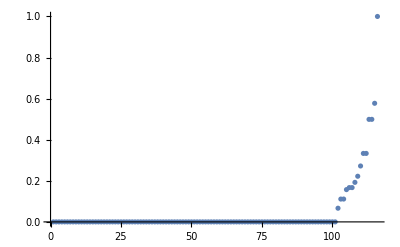

```mathematica
Abs@Chop[vars/.sol,10^-5];
ListPlot@Sort@%
```

```mathematica
Flatten@Position[Chop[vars/.sol,10^-5],0];
zeroes=Rule@@@Transpose@{vars⟦%⟧,ConstantArray[0,Length@%]};
```

```mathematica
zeroes
```

{x111111→0,x121111→0,x121112→0,x121113→0,x121213→0,x121313→0,x131112→0,x131212→0,x211111→0,x211121→0,x211131→0,x212121→0,x212131→0,x213131→0,x221111→0,x221112→0,x221113→0,x221121→0,x221122→0,x221123→0,x221131→0,x221132→0,x221133→0,x221213→0,x221221→0,x221222→0,x221223→0,x221231→0,x221232→0,x221233→0,x221313→0,x221321→0,x221322→0,x221323→0,x221331→0,x221332→0,x221333→0,x222121→0,x222122→0,x222123→0,x222131→0,x222132→0,x222133→0,x222223→0,x222232→0,x222323→0,x222331→0,x222332→0,x222333→0,x223132→0,x223232→0,x223233→0,x231112→0,x231121→0,x231122→0,x231131→0,x231132→0,x231212→0,x231221→0,x231222→0,x231231→0,x231232→0,x232121→0,x232122→0,x232131→0,x232132→0,x232222→0,x232231→0,x232232→0,x233131→0,x233132→0,x233232→0,x311111→0,x311121→0,x321111→0,x321112→0,x321113→0,x321121→0,x321122→0,x321123→0,x321212→0,x321213→0,x321221→0,x321222→0,x321223→0,x321313→0,x321321→0,x321322→0,x321323→0,x322122→0,x322123→0,x322222→0,x322223→0,x322323→0,x331112→0,x331121→0,x331212→0,x331221→0,x331222→0,x332121→0,x332122→0}

```mathematica
(* Guess for blocks p=4, q=1 *)
(*Block 2,3*)
v[2,3]=({{0, 0, 0, -(√15)/12, -(√5)/4, 0, 0, 0, (√(3/2))/2, -1/(2 √2), 0, 0, 0, -1/(6 √2), -1/(2 √6), 0, 0, 0, -1/12, -1/(4 √3)}, {(√15)/12, 0, 0, 0, 0, 0, 0, 0, 0, 0, -(8 √2)/12, 0, 0, 0, 0, 1/12, 0, 0, 0, 0}, {0, 0, 0, -1/4, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, (√15)/4, 0}, {0, 0, 0, (√15)/12, 0, 0, 0, 0, 0, 0, 0, 0, 0, -(2 √2)/3, 0, 0, 0, 0, 1/12, 0}, {1/4, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -(√15)/4, 0, 0, 0, 0}});
λs[2,3]={1,1/6,1/6,1/6,1/6};
B[2,3]=v[2,3]ᵀ.DiagonalMatrix[λs[2,3]].v[2,3]//FullSimplify;
(*Block 3,3*)
v[3,3]=({{3/8, (√3)/8, 0, (√3)/8, -1/8, -(√3)/8, 3/8, 0, 1/24, 1/(8 √3), 0, 0, 0, -1/(3 √2), -1/(√6), -(√3)/8, -1/8, 0, 3/8, -(√3)/8, -1/8, (√3)/8, 0, -1/(8 √3), -1/8}, {0, 0, 0, 0, 0, 0, 0, 0, -(√2)/3, 0, 0, 0, 0, -1/3, 0, 0, 0, 0, 0, 0, 0, 0, 0, √(2/3), 0}, {0, 0, 0, 0, 0, -(√2)/3, 0, 0, 0, 0, -1/3, 0, 0, 0, 0, 0, 0, 0, 0, 0, √(2/3), 0, 0, 0, 0}});
λs[3,3]={2,1/6,1/6};
B[3,3]=v[3,3]ᵀ.DiagonalMatrix[λs[3,3]].v[3,3]//FullSimplify;
(*Block 2,2*)
v[2,2]=({{0, -1/4, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, (√15)/4, 0, 0}, {0, -(√(5/3))/4, 0, 0, 0, 0, 0, 0, 0, (2 √2)/3, 0, 0, 0, -1/12, 0, 0}});
λs[2,2]={1/12,1/12};
B[2,2]=v[2,2]ᵀ.DiagonalMatrix[λs[2,2]].v[2,2]//FullSimplify;
(*Block 3,2*)
v[3,2]=({{0, 0, 0, 0, 0, -(√2)/3, 0, 0, 0, -1/3, 0, 0, 0, 0, 0, 0, 0, √(2/3), 0, 0}});
λs[3,2]={1/12};
B[3,2]=v[3,2]ᵀ.DiagonalMatrix[λs[3,2]].v[3,2]//FullSimplify;
B[1,1]=ConstantArray[0,{1,1}];
B[2,1]=ConstantArray[0,{4,4}];
B[3,1]=ConstantArray[0,{5,5}];
B[1,2]= ({{0, 0, 0, 0}, {0, 1/12, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});
B[1,3]= ({{1/6, 0, 0, 0, 0}, {0, 0, 0, 0, 0}, {0, 0, 0, 0, 0}, {0, 0, 0, 1/6, 0}, {0, 0, 0, 0, 0}});
```

```mathematica
guessAnsatz=Dispatch@Flatten@Table[Rule@@@Transpose@{Flatten[Table[x[λ,μ,i,j,k,l,irrepDims[p,q,d]],{i,1,irrepDims[p,q,d]⟦λ⟧},{k,1,irrepDims[p,q,d]⟦μ⟧},{j,1,irrepDims[p,q,d]⟦λ⟧},{l,1,irrepDims[p,q,d]⟦μ⟧}]],Flatten[B[λ,μ]]},{λ,1,Length@irrepDims[p,q,d]},{μ,1,Length@irrepDims[p,q,d]}];
```

```mathematica
blocks=Table[x[λ,μ,i,j,k,l,irrepDims[p,q,d]]/.elim/.sol,{λ,1,Length@irrepDims[p,q,d]},{μ,1,Length@irrepDims[p,q,d]},{i,1,irrepDims[p,q,d]⟦λ⟧},{k,1,irrepDims[p,q,d]⟦μ⟧},{j,1,irrepDims[p,q,d]⟦λ⟧},{l,1,irrepDims[p,q,d]⟦μ⟧}];
blocks=Flatten[Chop[blocks,10^-4],{{1},{2},{3,4},{5,6}}];
MatrixForm@Map[MatrixForm,blocks,{2}]
```

((0) | (0 | 0 | 0
0 | 0.16693 | 0
0 | 0 | 0) | (0.49921 | 0
0 | 0)
(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.166975 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.333333 | 0 | -0.272166 | 0 | 0.19245
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -0.272166 | 0 | 0.222223 | 0 | -0.157135
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.19245 | 0 | -0.157135 | 0 | 0.111111) | (0.499076 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)
(0 | 0
0 | 0.0665944) | (0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.111232 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0) | (1. | 0 | 0 | 0.57735
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0.57735 | 0 | 0 | 0.333332))

```mathematica
MatrixForm@Map[MatrixForm,Chop[Map[Eigenvalues,blocks,{2}],10^-5],{2}]
```

((0) | (0.16693
0
0) | (0.49921
0)
(0
0
0) | (0.666667
0.166975
0
0
0
0
0
0
0) | (0.499076
0
0
0
0
0)
(0.0665944
0) | (0.111232
0
0
0
0
0) | (1.33333
0
0
0))

```mathematica
(**)
```

((0) | (0.0833333
0
0
0) | (1/6
1/6
0
0
0)
(0
0
0
0) | (0.0833193
0.0833137
0.0000179256
0
0
0
0
0
0
0
0
0
0
0
0
0) | (0.999873
0.166696
0.166688
0.166684
0.166667
0.0000386387
0.0000358513
0.0000166359
0
0
0
0
0
0
0
0
0
0
0
0)
(0
0
0
0
0) | (0.0833126
0.0000179256
0.0000179256
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0) | (1.99968
0.166688
0.166687
0.0000812744
0.000038673
0.0000358513
0.0000356731
0.0000318115
0.0000103646
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0))

```mathematica
irrepDims[p,q,d]
```

{1,3,2}

```mathematica
A=Chop[ansatzNumeric/.sol];
```

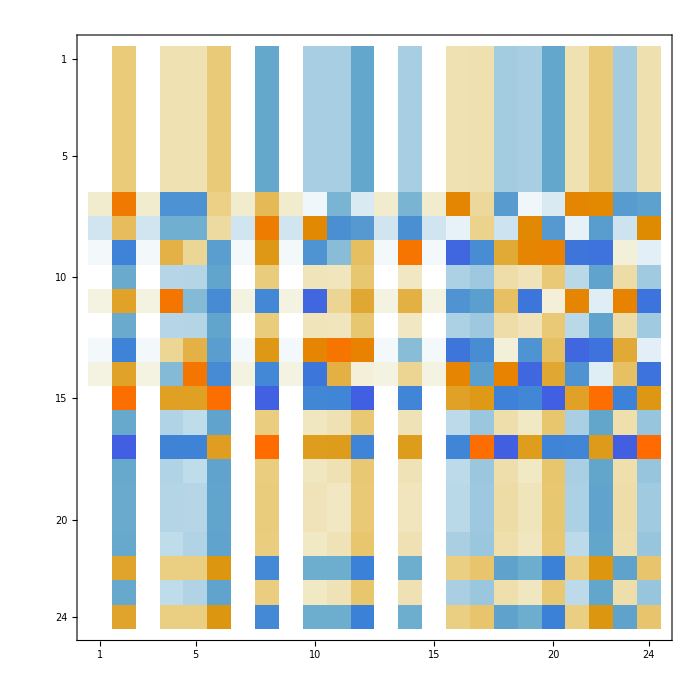

```mathematica
MatrixPlot@A
```